Exact calculation of the Josphson current in the U = 0 case
Rok Zitko, rok.zitko@ijs.si, Oct 2009
cf. Karrasch et al. PRB 2007

```mathematica
i=(1/(2Pi)) Δ Sin[ϕ]/(Cos[ϕ/2]^2+x^2(1+(Δ/Γ)y)^2+(ϵ/Γ)^2y^2)
i=i/.y->Sqrt[1+x^2]
params={ϵ->0,Δ->0.023076Γ,Γ->0.03847,ϕ->Pi/2}
gap=Δ//.params
i1=i//.params
exact=(2NIntegrate[i1,{x,0,∞}])/gap
```

(Δ Sin[ϕ])/(2 π (x^2 (1+(y Δ)/Γ)^2+(y^2 ϵ^2)/Γ^2+Cos[ϕ/2]^2))

(Δ Sin[ϕ])/(2 π (x^2 (1+(√(1+x^2) Δ)/Γ)^2+((1+x^2) ϵ^2)/Γ^2+Cos[ϕ/2]^2))

{ϵ→0,Δ→0.023076 Γ,Γ→0.03847,ϕ→π/2}

0.000887734

0.000141287/(1/2+x^2 (1+0.023076 √(1+x^2))^2)

0.655548

```mathematica
nrg=0.000582717/gap
error=nrg/exact
```

0.65641

1.00131

```mathematica
calc[phi_]:=Module[{},
i=(1/(2Pi)) Δ Sin[ϕ]/(Cos[ϕ/2]^2+x^2(1+(Δ/Γ)y)^2+(ϵ/Γ)^2y^2);
i=i/.y->Sqrt[1+x^2];
params={ϵ->0,Δ->0.023076Γ,Γ->0.03847,ϕ->phi};
i1=i//.params;
(2NIntegrate[i1,{x,0,∞}])/gap
];
```

```mathematica
t=Table[{phi,calc[phi]},{phi,0,Pi,Pi/50}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.501431}. NIntegrate obtained 0. and 0. for the integral and error estimates.

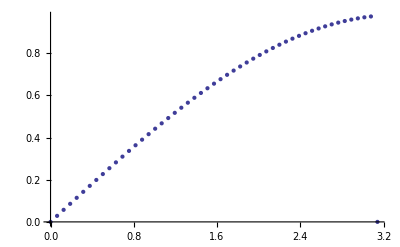

```mathematica
ListPlot[t]
```

```mathematica
calc[Pi 0.99]
```

0.975962